## Lab 6 Francesco Vassalli

### Introduction

Diodes, photodiodes, and light emitting diodes (LEDs) are a few examples of semiconductors which are foundational in modern electronics.  A LED circuit can convert some electrical power into light, conversely the photodiode allows current to flow in a reverse bias setup when it absorbs light energy.  We provide examples of the utility of these devices by constructing a photodiode circuit and comparing its response to prediction for our lab lighting, constructing a LED circuit that emits light, and recording the response of our photodiode to our LED as a function of distance.

### Experiment

#### Photodiode

-Graphics-

Schematic of the photodiode circuit. We make an inverting op-amp but replace the voltage source with the photodiode.

S_λ=s(λ)R_(940nm)

ΔV_out/(R_F S_λ)=N

-Graphics-

The relative spectral sensitivity (s) simultaneously provides a conversion factor from the light sensitivity of the photodiode to power and the correction for the frequency of the light.  R_(940nm) is determined by the physical properties of the photodiode.

N=[light power per solid angle]/(α(λ)R^2)

-Graphics-

The α factor in equation 3 simultaneously provides a conversion factor from the power of the light bulb to the sensitivity of the photodiode and the correction for the frequency of the light.  The frequency dependence is depicted in the plot above which is multiplied by 683 mW/mc.

```mathematica
Grid[{{"λ","550nm"},{"R_(940  nm)","10μAcm^2/mW"},{"s_λ","6.8μAcm^2/mW"},{"R_F","1.502MΩ"},{"C_F","5.8pF"},{"ΔV_out","1.6V"},{"N_measured","0.16mW/cm^2"},{"N_predicted","0.1mW/cm^2"}},Frame->All]
```

λ | 550nm
R_(940  nm) | 10μAcm^2/mW
s_λ | 6.8μAcm^2/mW
R_F | 1.502MΩ
C_F | 5.8pF
ΔV_out | 1.6V
N_measured | 0.16mW/cm^2
N_predicted | 0.1mW/cm^2

The inverting op-amp provides a familiar vector for measuring voltage response.  To find the power of light in the room we cover the photodiode and record V_out we move the photodiode to be in full view of the light and measure V_out. Using equation 2 yields N_measuredwhile equation 3 yields N_predicted.  The prediction has many variables that are hard to control such as light pollution so we conclude that the data agrees. N measures the mW/cm^2 at the distance of the photodiode.

#### LED and Photo-Distance Response

-Graphics-

Schematic of the LED circuit.

-Graphics-

Schematic of the inverting op-amp circuit.

```mathematica
Grid[{{"f_(3  db) direct","18.629"},{"f_(3  dB) photodiode","18.09"}},Frame->All]
```

f_(3  db) direct | 18.629
f_(3  dB) photodiode | 18.09

We construct the LED and an inverting op-amp circuit and measure the f_(3dB) of the op-amp. Using the same op-amp we construct the photodiode circuit and place the LED 2cm from the photodiode with a square wave into the photodiode.  We separate the LED signal from the room light background by subtracting the DC offset.  We make a new measurement of the f_(3dB)by measuring the rise time. This agrees with our original measurement.

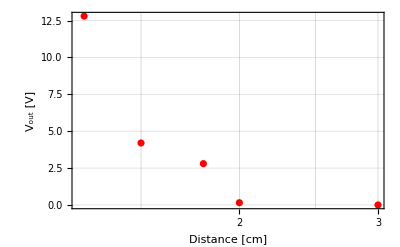

```mathematica
λ={1.27,2,3,1.8,1.5};
v={12.8,.152,0,2.8,4.2};
ListPlot[Thread[{λ,v}],
ScalingFunctions->{"Log"},
Frame->True,Axes->True,
LabelStyle->{FontFamily->"Arial", FontSize->13},
FrameLabel->{"Distance [cm]","V_out [V]"},
FrameStyle->Thickness[.005],PlotStyle->{Red,Thickness[.01]},GridLines->Automatic]
```

Voltage response of the op-amp circuit as a function of distance between the LED and the photodiode.

The voltage response with respect to distance follows roughly 1/r^2which is the expected behavior.

### Conclusion

The photodiode circuit has the expected behavior for sensitivity to room lighting, cutoff frequency for LED signal, and changing signal distance. The models for predicting photodiode response are sensitive to many variables for a refined model it is best to control all lighting distance, wavelength, and intensity.